```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/2.1.6.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/f2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6(2).xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6.xlsx}

```mathematica
importfile = files⟦3⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6(2).xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line1=LinearModelFit[Normal@dataset1[All,{"P","DT"}/*Values],{1,x},x]
line1["ParameterTable"]
```

FittedModel[2.47891+0.0100824 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.47891 | 0.0794061 | 31.2182 | 6.33147×10^-7
x | 0.0100824 | 0.000302359 | 33.3459 | 4.55951×10^-7

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line2=LinearModelFit[Normal@dataset2[All,{"P","DT"}/*Values],{1,x},x]
line2["ParameterTable"]
```

FittedModel[2.20359+0.00982854 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.20359 | 0.0341078 | 64.6066 | 1.68192×10^-8
x | 0.00982854 | 0.00013092 | 75.0729 | 7.94444×10^-9

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset3WithErrs=dataset3[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line3=LinearModelFit[Normal@dataset3[All,{"P","DT"}/*Values],{1,x},x]
line3["ParameterTable"]
```

FittedModel[1.71958+0.00978707 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.71958 | 0.0677767 | 25.3713 | 1.77579×10^-6
x | 0.00978707 | 0.000258876 | 37.806 | 2.43922×10^-7

## Dataset4

```mathematica
dataset4=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset4WithErrs=dataset4[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line4=LinearModelFit[Normal@dataset4[All,{"P","DT"}/*Values],{1,x},x]
line4["ParameterTable"]
```

FittedModel[1.60714+0.00819971 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.60714 | 0.0254909 | 63.0478 | 1.90013×10^-8
x | 0.00819971 | 0.0000966027 | 84.8807 | 4.30143×10^-9

## Dataset5

```mathematica
dataset5=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset5WithErrs=dataset5[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line5=LinearModelFit[Normal@dataset5[All,{"P","DT"}/*Values],{1,x},x]
line5["ParameterTable"]
```

FittedModel[1.15165+0.0083813 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.15165 | 0.0323307 | 35.6211 | 3.28178×10^-7
x | 0.0083813 | 0.000121557 | 68.9494 | 1.21528×10^-8

## Dataset6

```mathematica
dataset6=makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
dataset6WithErrs=dataset6[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line6=LinearModelFit[Normal@dataset6[All,{"P","DT"}/*Values],{1,x},x]
line6["ParameterTable"]
```

FittedModel[0.886851+0.00746428 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.886851 | 0.0436207 | 20.331 | 5.32502×10^-6
x | 0.00746428 | 0.000164006 | 45.5123 | 9.66972×10^-8

## Dataset7

```mathematica
dataset7=makeDataset[raw⟦7⟧]
```

Dataset[<>]

```mathematica
dataset7WithErrs=dataset7[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line7=LinearModelFit[Normal@dataset7[All,{"P","DT"}/*Values],{1,x},x]
line7["ParameterTable"]
```

FittedModel[0.560962+0.00691102 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.560962 | 0.0361912 | 15.5 | 0.000020299
x | 0.00691102 | 0.000136072 | 50.7893 | 5.59292×10^-8

## Dataset8

```mathematica
dataset8=makeDataset[raw⟦8⟧]
```

Dataset[<>]

```mathematica
dataset8WithErrs=dataset8[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line8=LinearModelFit[Normal@dataset8[All,{"P","DT"}/*Values],{1,x},x]
line8["ParameterTable"]
```

FittedModel[0.285158+0.00594202 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.285158 | 0.0338367 | 8.42746 | 0.000385867
x | 0.00594202 | 0.00012722 | 46.7067 | 8.49719×10^-8

## Ура, график

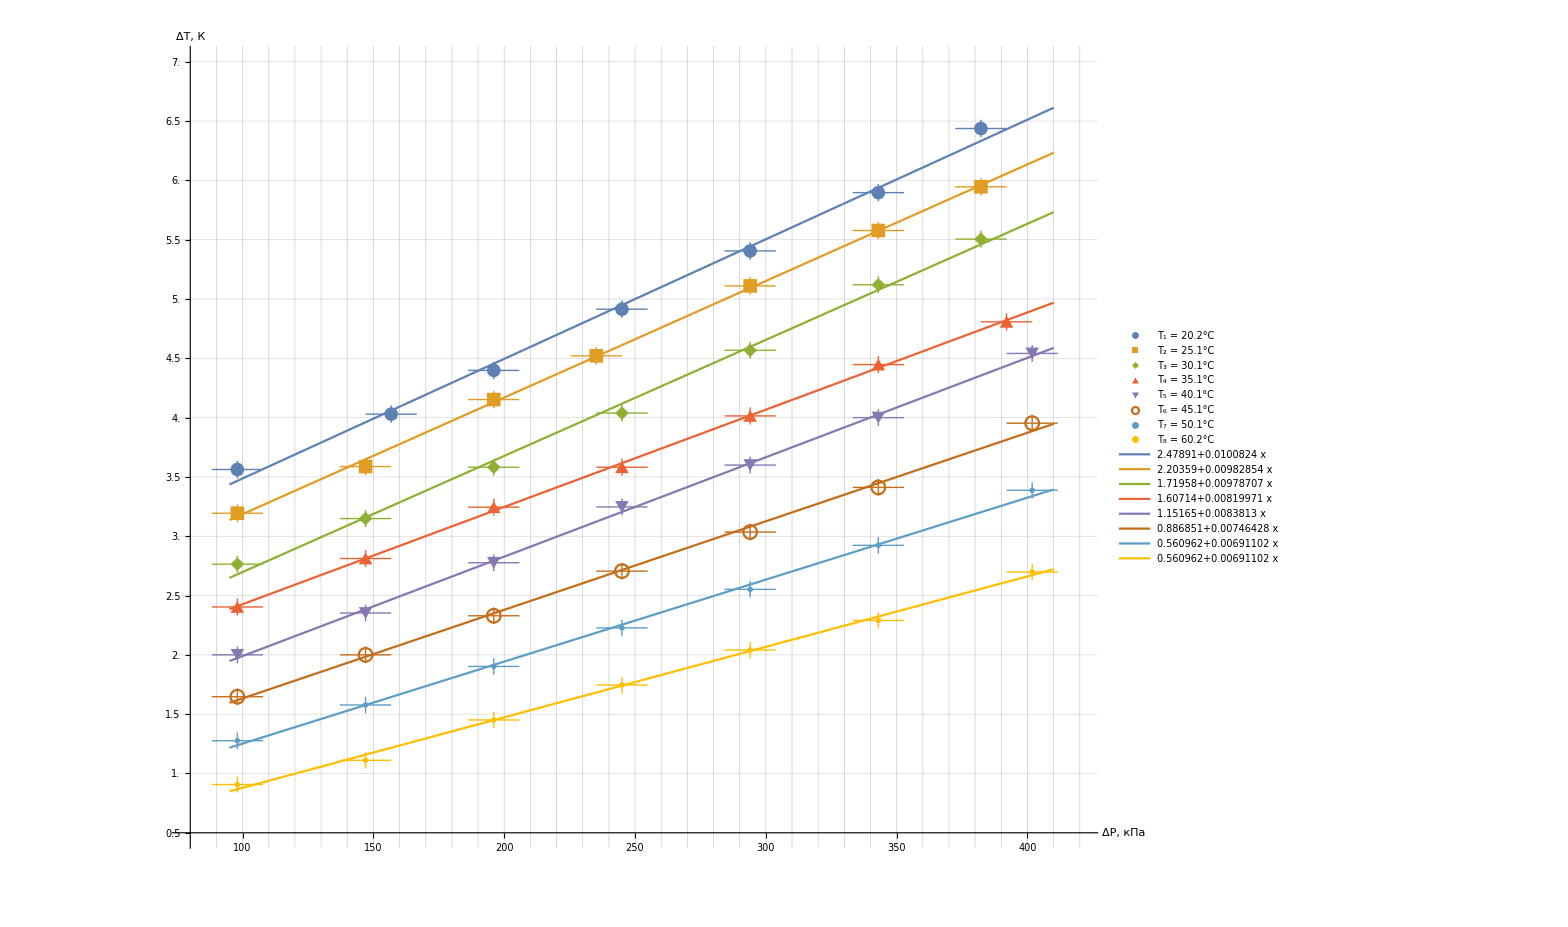

```mathematica
Show[
ListPlot[{dataset1WithErrs,dataset2WithErrs,dataset3WithErrs,dataset4WithErrs,dataset5WithErrs,dataset6WithErrs,dataset7WithErrs,dataset8WithErrs},
AxesLabel->{Style["ΔP, кПа",Large],Style["ΔT, К",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,10], Range[0,10,0.25]},
Ticks-> {Range[0,420,50],Range[0,8,0.5]}, 
TicksStyle->20,
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{80,420},{0.5,7}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"T_1 = 20.2°C","T_2 = 25.1°C","T_3 = 30.1°C","T_4 = 35.1°C","T_5 = 40.1°C","T_6 = 45.1°C","T_7 = 50.1°C","T_8 = 60.2°C"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Row"
],
{Scaled[0.8],Scaled[0.12]}
]
],
Plot[
{line1@x,line2@x,line3@x,line4@x,line5@x,line6@x,line7@x,line8@x},{x,95,410}, (*Вот тут вопрос: почему нельзя чистой функцией?*)
(*PlotStyle->Thickness[0.002]*)
PlotLegends->Placed[
LineLegend
[
Automatic,
Normal/@{line1,line2,line3,line4,line5,line6,line7,line7,line8},
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.2],Scaled[0.75]}
]
]
]
```

```mathematica
Show[
Plot[#[x]&/@{line1,line2,line3},{x,100,400},PlotStyle->"Rainbow"]
]
```

-Graphics-

## Вторая часть графика

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/2.1.6.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/f2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6(2).xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6.xlsx}

```mathematica
importfile = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/f2.xlsx

```mathematica
raw2 = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
mydataset=makeDataset[raw2⟦1⟧]
```

Dataset[<>]

```mathematica
tolabel = mydataset[All,<|"1/T"->"1/T","dt"->"dt"|>]
```

Dataset[<>]

```mathematica
mydatasetWithErrs=mydataset[All,<|"1/T"->"1/T","dt"->(Around[#dt,#sigma]&)|>]
```

Dataset[<>]

```mathematica
myline=LinearModelFit[Normal@mydataset[All,{"1/T","dt"}/*Values],{1,x},x]
myline["ParameterTable"]
```

FittedModel[-20.6164+9.02742 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -20.6164 | 3.91003 | -5.27269 | 0.00187836
x | 9.02742 | 1.21404 | 7.43586 | 0.000304592

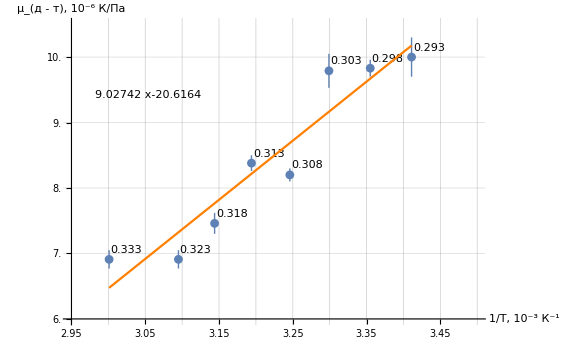

```mathematica
Show[
ListPlot[Labeled[#,NumberForm[1/#@"1/T",3]]&/@mydatasetWithErrs,
AxesLabel->{Style["1/T, 10^-3 (:041a)^-1",Medium],Style["μ_(:0434 - :0442), 10^-6 К/Па",Medium]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->Large,
GridLines->{Range[2.9,4,0.05], Range[0,12,0.25]},
Ticks-> {Range[2.95,3.6,0.1],Range[6,12,0.5]}, 
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{2.95,3.5},{6,10.5}}
],
Plot[myline@x,{x,mydatasetWithErrs[-1,"1/T"],mydatasetWithErrs[1,"1/T"]},
PlotStyle->Orange,
PlotLegends->Placed[Normal[myline],{Scaled[0.2],Scaled[0.75]}]
]
]
```

```mathematica
mydatasetWithErrs[{;;3}, {"1/T","dt"}/*Values]
```

Dataset[<>]

```mathematica
myline3=LinearModelFit[Normal@mydataset[;;3,{"1/T","dt"}/*Values],{1,x},x]
myline3["ParameterTable"]
```

FittedModel[3.58271+1.875 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.58271 | 2.24852 | 1.59336 | 0.356806
x | 1.875 | 0.670139 | 2.79793 | 0.218525

```mathematica
Labeled[#,NumberForm[1/#@"1/T",3]]&
```

#11/(Slot[1][1/T])&

```mathematica
Show[
ListPlot[Labeled[#,#/@[NumberForm/@{"T_1 = 20.2°C","T_2 = 25.1°C","T_3 = 30.1°C","T_4 = 35.1°C","T_5 = 40.1°C","T_6 = 45.1°C","T_7 = 50.1°C","T_8 = 60.2°C"}]]&/@mydatasetWithErrs,
AxesLabel->{Style["1/T, 10^-3 (:041a)^-1",Medium],Style["μ_(:0434 - :0442), 10^-6 К/Па",Medium]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->Large,
GridLines->{Range[2.9,4,0.05], Range[0,12,0.25]},
Ticks-> {Range[2.95,3.6,0.1],Range[6,12,0.5]}, 
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{2.95,3.5},{6,10.5}}
],
Plot[myline@x,{x,mydatasetWithErrs[-1,"1/T"],mydatasetWithErrs[1,"1/T"]},
PlotStyle->Orange,
PlotLegends->Placed[Normal[myline],{Scaled[0.2],Scaled[0.75]}]
]
]
```

Syntax::sntxf: "#/@" cannot be followed by "[NumberForm/@{T_1 = 20.2°C,T_2 = 25.1°C,T_3 = 30.1°C,T_4 = 35.1°C,T_5 = 40.1°C,T_6 = 45.1°C,T_7 = 50.1°C,T_8 = 60.2°C}]".

```mathematica
temperature = {"T_1 = 20.2°C","T_2 = 25.1°C","T_3 = 30.1°C","T_4 = 35.1°C","T_5 = 40.1°C","T_6 = 45.1°C","T_7 = 50.1°C","T_8 = 60.2°C"}
```

{T_1 = 20.2°C,T_2 = 25.1°C,T_3 = 30.1°C,T_4 = 35.1°C,T_5 = 40.1°C,T_6 = 45.1°C,T_7 = 50.1°C,T_8 = 60.2°C}

```mathematica
/@
```

Function::slotn: Slot number 2 in #1& cannot be filled from (#1&)[Dataset[«8»]].

ListPlot::lpn: Map[Dataset] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

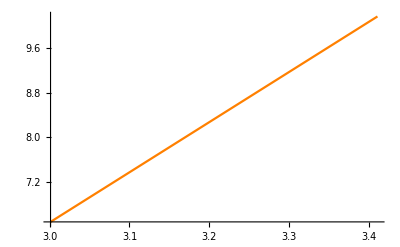
Show[ListPlot[Map[Dataset[<>]#2],AxesLabel→{1/T, 10^-3 К^-1,μ_(д - т), 10^-6 К/Па},AxesStyle→Directive[Arrowheads[{0.02}],GrayLevel[0]],ImageSize→Large,GridLines→{{2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.},{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.,10.25,10.5,10.75,11.,11.25,11.5,11.75,12.}},Ticks→{{2.95,3.05,3.15,3.25,3.35,3.45,3.55},{6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.}},PlotRange→{{2.95,3.5},{6,10.5}}],-Graphics-]

```mathematica
Show[
ListPlot[Map[Labeled[#,#2]&[mydatasetWithErrs]]& [Map[{"T_1 = 20.2°C","T_2 = 25.1°C","T_3 = 30.1°C","T_4 = 35.1°C","T_5 = 40.1°C","T_6 = 45.1°C","T_7 = 50.1°C","T_8 = 60.2°C"}]],
AxesLabel->{Style["1/T, 10^-3 (:041a)^-1",Medium],Style["μ_(:0434 - :0442), 10^-6 К/Па",Medium]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->Large,
GridLines->{Range[2.9,4,0.05], Range[0,12,0.25]},
Ticks-> {Range[2.95,3.6,0.1],Range[6,12,0.5]}, 
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{2.95,3.5},{6,10.5}}
],
Plot[myline@x,{x,mydatasetWithErrs[-1,"1/T"],mydatasetWithErrs[1,"1/T"]},
PlotStyle->Orange,
PlotLegends->Placed[Normal[myline],{Scaled[0.2],Scaled[0.75]}]
]
]
```